# All contributung processes

```mathematica
Clear[fa23BsMix]
```

```mathematica
(*constraints and constants*)
GF = 1.16*^-5;
aEM = 1/137;
lambda = 0.22;
mu = 0.105;
Ncm = 1;
Ncq = 3;

C9low1f = -0.71;
C9high1f = -0.35;
C9low2f = -0.91;
C9high2f = -0.18;
bsmix = 2.5*^-11;
annRate = 6.9*^-9;
abest = 2.87*^-9;
alow = 2.07*^-9;
ahigh = 3.67*^-9;

mldiff = 200; (*16.08: appears to be good: minimal because of slepton exclusions and maximal due to annihilation*)
mqdiff = 800;
gq2f = 0.3;
gq3f = 0.3;
gl2f = 0.9;
```

```mathematica
(*only for g-2; gl,m,Ml*)
tda[m_,M_]:=m^2/M^2 (*In Lavoura: t:=m^2/M^2 (t<1) but elsewhere t=M^2/m^2 because we have two Ms!*)
d[t_]:= (-2t^2+7-11)/(18(t-1)^3)+(Log[t])/(3(t-1)^4)
dbar[t_]:=d[t]/t
c[t_]:= (t-3)/(4(t-1)^4)+(Log[t])/(2(t-1)^3) 
cbar[t_]:=-c[t]/t
pda[g_,m_]:= g^2*mu^2/(16*Pi^2) * 1/(m+mldiff)^2
da[g_,m_,Qf_,Qb_]:=pda[g,m]*(Qf*(c[tda[m,m+mldiff]]+3/2*d[tda[m,m+mldiff]])+ Qb*(-cbar[tda[m,m+mldiff]]+3/2*dbar[tda[m,m+mldiff]]))
da[1,200,0,-1]
```

3.32623×10^-9

```mathematica
(*Annihilation, for now only into muons*)
annl[g_,m_,Nc_]:=Nc * g^4/(32*Pi)* m^2/((m+mldiff)^2+m^2)^2;
annq[g1_,g2_,m_,Nc_]:=Nc * (g1^2+g2^2)^2/(32*Pi) * m^2/((m+mqdiff)^2+m^2)^2;
annTot[gl2_,gq2_,gq3_,m_,Nq_,Nl_]:=annl[gl2,m,Nl]+annq[gq2,gq3,m,Nq]
```

```mathematica
(*Bs->mumu*)
xHad[m_,M_]:=M^2/m^2 (*Here t>1*)
Kshort[x_]:= (1-x+x^2Log[x])/(x-1)^2;
Kder[x_]:=(-1+x^2-2*x*Log[x])/(x-1)^3
Klong[x_,y_]:= (Kshort[x]-Kshort[y])/(x-y)
weak=4*GF/Sqrt[2]*(-1)*lambda^2*aEM/(4Pi);

fa23[pMod_,C_,m_,gm_]:=C*weak/pMod * m^2 /gm^2 * 1/Klong[xHad[m,m+mqdiff],xHad[m,m+mldiff]];
fa23BsMix[pMod_,m_]:=bsmix*m^2/(pMod *Kder[xHad[m,m+mqdiff]]);
```

## modA

## modB

```mathematica
preB=5/(384Pi^ 2);
fa23[preB,C9high1f,100,1]
gl2f
```

0.0959305

0.9

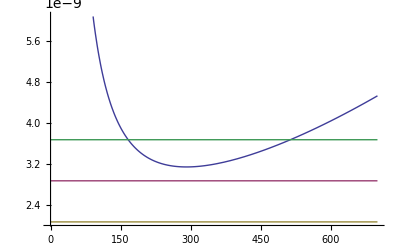

```mathematica
Plot[{da[gl2f,m,-1,0]+da[gl2f,m,0,-1],abest,alow,ahigh},{m,0,700}]
(*effects: Ml higher -> lowers blue line (allowed region rise)   *)
(*         Mq higher -> almowst no effect for small gqs          *)
```

```mathematica
FindRoot[da[gl2f,m,-1,0]+da[gl2f,m,0,-1]==ahigh,{m,100}]
```

{m→166.25}

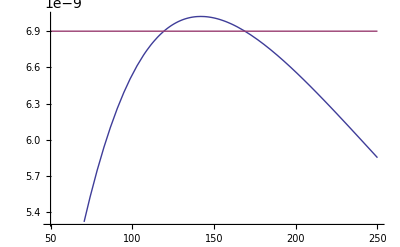

```mathematica
Plot[{annTot[gl2f,gq2f,gq3f,m,Ncq,Ncm],annRate},{m,50,250}] 
(*effects: Ml higher -> lowers strongly blue line (allowed region shrinks)*)
(*         Mq higher -> almowst no effect for small gqs          *)
```

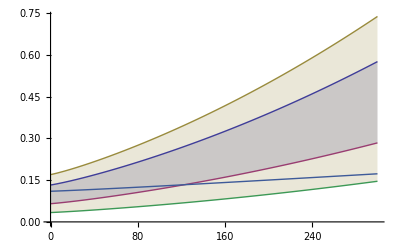

```mathematica
Plot[{fa23[preB,C9low1f,m,gl2f],fa23[preB,C9high1f,m,gl2f],fa23[preB,C9low2f,m,gl2f],fa23[preB,C9high2f,m,gl2f],Sqrt[fa23BsMix[preB,m]]},{m,0,300},Filling-> {1->{2},3->{4}}]
```

```mathematica
FindRoot[Sqrt[fa23BsMix[preB,m]]==fa23[preB,C9high1f,m,gl2f],{m,120}]
```

{m→122.679}